```mathematica
Sum[DJn[0.1,n],{n,0,40}]
```

0.74418

```mathematica
DJn[x_,m_] := (1/2)^m Sum[(-1)^l(m!)/(l!(m-l)!)BesselJ[-m+2 l,x],{l,0,m}]//N
```

```mathematica
DJn[1,40]
```

0.0690017

```mathematica
error[x_,m_,σ_] := 1/((2m)!)((1+x)Sum[DJn[x,n],{n,0,2 m}]+x DJn[x,2m])Exp[x-x^2/(4 σ^2)]
```

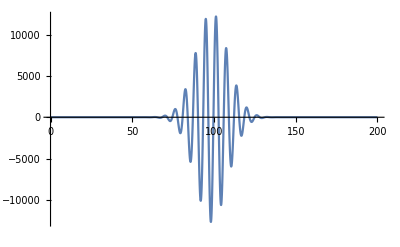

```mathematica
Plot[error[x,10,7],{x,0.01,200},PlotRange->All]
```

```mathematica
Integrate[LegendreP[2,x] LegendreP[2,x],{x,-1,1}]
```

2/5

16 ⅇ^(-4 (1+x)^2) (1+x) σ^2 BesselJ[0,4 (1+x) σ]

```mathematica
f[x_,σ_] = (2 σ)^2(x+1)BesselJ[0,2 σ(x+1)]Exp[-(x+1)^2]
fp[x_,σ_,n_] := Abs[1/((2 n)!)2/(2n+2)D[f[y,σ],{y,2 n}]]/.y-> x
```

4 ⅇ^(-(1+x)^2) (1+x) σ^2 BesselJ[0,2 (1+x) σ]

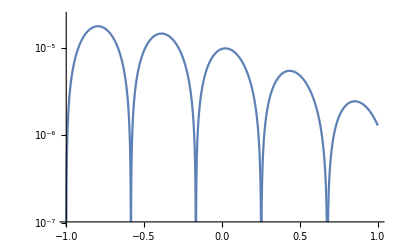

```mathematica
LogPlot[fp[x,1,10],{x,-1,1}]
```